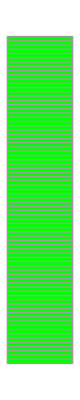
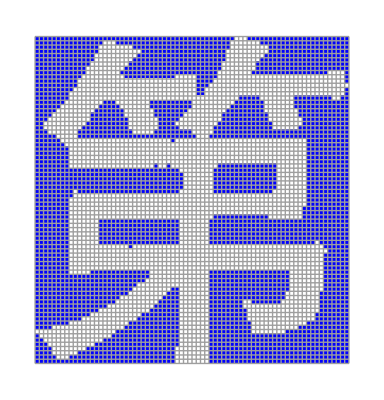
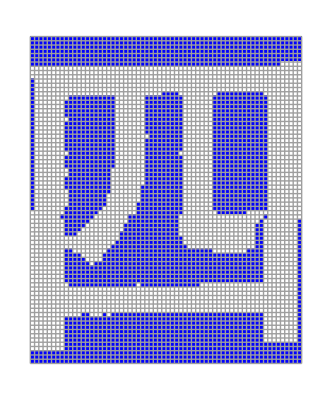
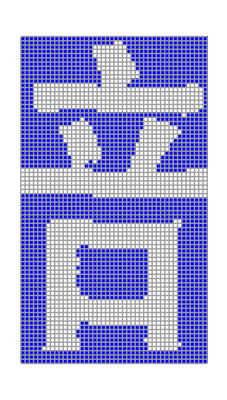
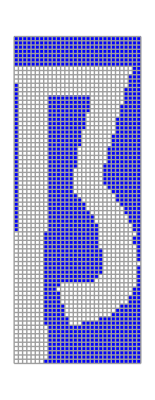
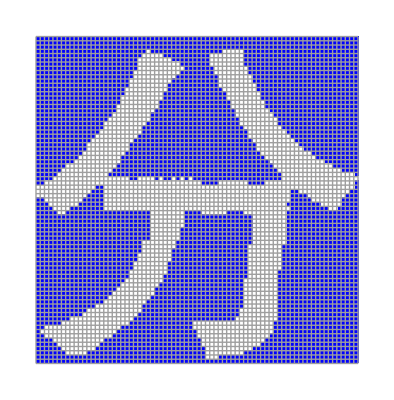
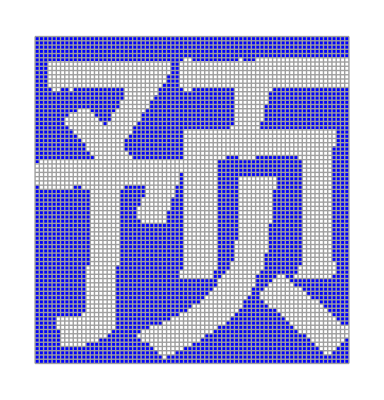
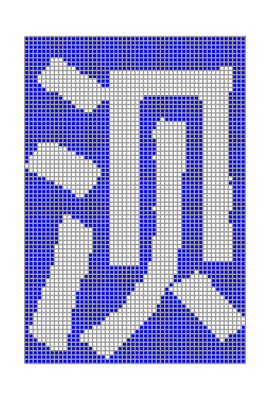
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i2//segment//First//splitByGreen//plot/@#&
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Get@"Skew.wl"
```

```mathematica
Get@"Segment.wl"
```

```mathematica
$ContextPath
```

{Segment`,Skew`,Parallel`Debug`Perfmon`,Parallel`Debug`,JLink`,TemplatingLoader`,PacletManager`,System`,Global`}

```mathematica
plot:=ArrayPlot[#,ColorRules->{0->Blue,1->White,2->Red,3->Green},Mesh->All]&(*全黑会画成全白，坑了。用蓝代替黑*)
```

```mathematica
i=Import@"data/01.png"
```

-Graphics-

```mathematica
(*//Flatten[#,1]*)
```

```mathematica
(*i//segmentSmart//(plot/@#&)/@#&;*)
```

```mathematica
(*i//segmentSmart//First//plot/@#&*)
```

```mathematica
(*mtRedTrunBlack[mt_]:=mt/.{x:2..}:>({x}/.{2->0})*)
```

```mathematica
(*RedTrunBlack[mt_]:=mt//Transpose//mtRedTrunBlack//Transpose*)
```

```mathematica
(*i//segmentSmart//First//plot/@#&*)
```

```mathematica
(*i//segmentSmart//First//RedTrunBlack/@#&//plot/@#&*)
(*i//segmentSmart//(RedTrunBlack/@#&)/@#&//(plot/@#&)/@#&*)
```

```mathematica
(*i//segmentSmart//(RedTrunBlack/@#&)/@#&//mergeSplitBy/@#&//plot/@#&*)
```

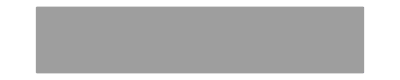
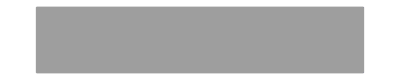
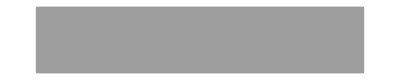
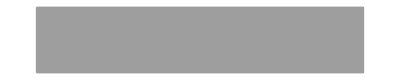
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i//segmentAndPlot
```

```mathematica
i//segment//First//plot
```

-Graphics-

```mathematica
ocrChinese[i_]:=TextRecognize[i,Language->"Chinese","SegmentationMode"->7]
```

```mathematica
imageBin[mt_]:=Image[mt,"Bit",Magnification->1]//ImageResize[#, Scaled[5]]&
```

```mathematica
(*splitByGreen[mt_]:=mt//Transpose//SplitBy[#,MatchQ[#,{3..}]&]&//Transpose/@#&*)
```

```mathematica
i//segment//First//splitByGreenClean//imageBin/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i//segment//First//splitByGreenClean//imageBin/@#&//ocrChinese/@#&
```

{长,久,以,来,!',机,器,视,觉,认,知,íl-,直,是,人,们,研,究,的,热,点,‘l',它,是,研,究,使,用,机,器,或,:í/十,算}

```mathematica
i//segment//First//splitByGreenClean//imageBin/@#&//ImageData/@#&//mergeSplitBy//Image//ColorNegate
```

-Graphics-

```mathematica
-Graphics-//ocrChinese
```

安全生产违法行为的法律责

```mathematica
i2=Import@"data/simple01.bmp";
```

```mathematica
(*i2//Binarize//Export@@{"data/simple02.bmp",#}&;*)
```

```mathematica
i2
```

-Graphics-

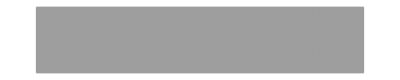
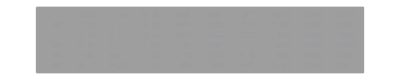
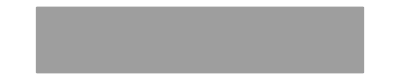
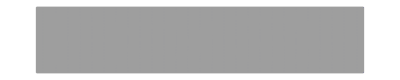
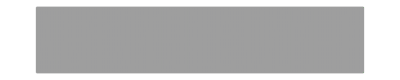
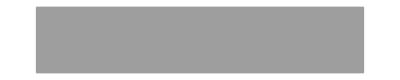
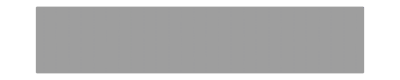
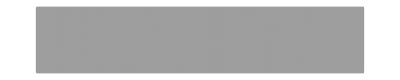
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i2//segmentAndPlot
```

```mathematica
i2//segment//First//splitByGreenClean//imageBin/@#&//ImageData/@#&//mergeSplitBy//Image//ColorNegate
```

-Graphics-

```mathematica
i2//segment//First//splitByGreen//plot/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i2//segment//First//plot
```

-Graphics-

```mathematica
i2//segment//First//splitByGreen//plot/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentByHorizon@i2//ocrChinese/@#&//TableForm
```

第四部分 预测试卷
预测试卷( 一)
一、单1页选择题(共7O 题,每题1 分〇 每题的备选项中,只有 1 个最符合题意)
1. 下列关于法律规范的表述,错误的是( 〉0
A. 法律规范是社会规范的一种
B. 法律规范反映由一定的物质生活条件所决定的统治阶级的意志
C- 法律规范不一定采用正式文件的形式
D- 法律规范是一般行为规则
2- 行政机关实施行政管理 , 除涉及国家秘密和依法受到保护的商业秘密 、个人隐私的 以外,
应当注意公开听取公民 、法人和其他组织的意见〇 这体现了依法行政的( )要求〇
A- 程序正当 B. 合法行政
C- 权责统一 D. 高效便民
3. 下列属于行政法规的是( )0
A_  》 B. 《民用航空法》
C- 《标准化法》 D- 《安全生产许可证条例》
4_ 居于安全生产法律体系最高层级的是( 〉0
A. 法律 B. 行政法规
C. 地方性法规 D- 部 门规章
5- 依据《安全生产法》 和《标准化法》 的规定 , 涉及安全生产方面的标准主要有 国家标准和
行业标准 ,其中多数是( )标准0
A~ 程序性 B. 强制性
C- 应用性 D. 规范性
6- 《安全生产法》规定的安全生产违法行为的法律责任形式 ,包括( )0
A- 行政责任和刑事责任 B- 宪法责任 、行政责任和刑事责任
C. 司法责任和民事责任 D- 行政责任、民事责任和刑事责任
7. 依据《 安全生产法》 的规定 , 生产经营单位( )对本单位的安全生产全面负 责 , 负 责安
全生产重大事项 的决策并组织实施 0
A- 主要负责人 B- 安全生产管理人员
C- 班组长 D- 从业人员
8- 依据《安全生产法》 的规定 , 生产经营单位的( )人员 必须按照 国家有关规定经专 门
的安全作业培训 ,取得该作业操作资格证书 ,方可上岗作业0
A. 专业技术 B. 安全生产管理